{1.22,1.4884,1.81585,2.21533,2.70271,3.2973,4.02271,4.90771,5.9874,7.30463}

{1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906}

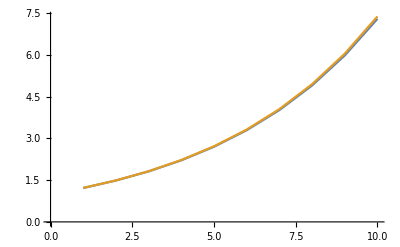

{0.00140276,0.0034247,0.0062708,0.0102064,0.0155737,0.022813,0.0324891,0.0453252,0.0622447,0.0844247}

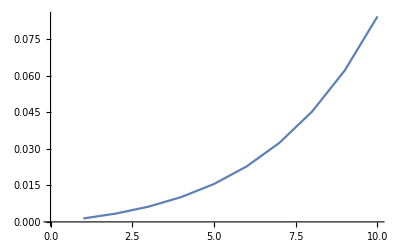

```mathematica
(*William Rodrigues


MidPoint*)
x0=0;
u0=1;
dx=0.1;
a=2;

u[x_]:=Exp[2x];
f[x_]:=Derivative[u[x],x];


unplus1={};
For[i=1,i≤10,i++,
t=u0+a*(u0+a*u0*dx/2)*dx;
u0=t;
AppendTo[unplus1,t];
];
unplus1

actun={};
For[i=0.1,i≤1,i=i+.1,
AppendTo[actun,u[i]];
];
actun

ListLinePlot[{unplus1,actun}]

errorr={};
For[i=1,i≤10,i++,
q=Abs[unplus1[[i]]-actun[[i]]];
AppendTo[errorr,q];
];
errorr
ListLinePlot[errorr]
```

```mathematica
(*Shooting*)


T=3;
k=0.23;
L=0.25;
dx=0.01;
u0=4.5;
uL=3;

vd=k((u0^4)-(T^4));
vs={};
us={};
For[i=dx,i<L,i=i+0.01,

v=v0+dx*vd;
u=u0+dx*v0;
(*Dont understand how to find the v0*)

u0=u;
vd=k((u0^4)-(T^4));
AppendTo[vs,v];
AppendTo[us,u];

];
vs
us
```

{0.756844+v0,0.0023 (-81+(4.5+0.01 v0)^4)+v0,0.0023 (-81+(4.5+0.02 v0)^4)+v0,0.0023 (-81+(4.5+0.03 v0)^4)+v0,0.0023 (-81+(4.5+0.04 v0)^4)+v0,0.0023 (-81+(4.5+0.05 v0)^4)+v0,0.0023 (-81+(4.5+0.06 v0)^4)+v0,0.0023 (-81+(4.5+0.07 v0)^4)+v0,0.0023 (-81+(4.5+0.08 v0)^4)+v0,0.0023 (-81+(4.5+0.09 v0)^4)+v0,0.0023 (-81+(4.5+0.1 v0)^4)+v0,0.0023 (-81+(4.5+0.11 v0)^4)+v0,0.0023 (-81+(4.5+0.12 v0)^4)+v0,0.0023 (-81+(4.5+0.13 v0)^4)+v0,0.0023 (-81+(4.5+0.14 v0)^4)+v0,0.0023 (-81+(4.5+0.15 v0)^4)+v0,0.0023 (-81+(4.5+0.16 v0)^4)+v0,0.0023 (-81+(4.5+0.17 v0)^4)+v0,0.0023 (-81+(4.5+0.18 v0)^4)+v0,0.0023 (-81+(4.5+0.19 v0)^4)+v0,0.0023 (-81+(4.5+0.2 v0)^4)+v0,0.0023 (-81+(4.5+0.21 v0)^4)+v0,0.0023 (-81+(4.5+0.22 v0)^4)+v0,0.0023 (-81+(4.5+0.23 v0)^4)+v0}

{4.5+0.01 v0,4.5+0.02 v0,4.5+0.03 v0,4.5+0.04 v0,4.5+0.05 v0,4.5+0.06 v0,4.5+0.07 v0,4.5+0.08 v0,4.5+0.09 v0,4.5+0.1 v0,4.5+0.11 v0,4.5+0.12 v0,4.5+0.13 v0,4.5+0.14 v0,4.5+0.15 v0,4.5+0.16 v0,4.5+0.17 v0,4.5+0.18 v0,4.5+0.19 v0,4.5+0.2 v0,4.5+0.21 v0,4.5+0.22 v0,4.5+0.23 v0,4.5+0.24 v0}